# Generating Training Data

## Tyson Jones tyson.jones@monash.edu July 2017

## Random Potentials

```mathematica
Clear["Global`*"]
PacletDirectoryAdd[NotebookDirectory[]];
<< EigenFunctions`
```

## potential ceiling

### theoretical discussion

Scaling space by α in the Schrodinger equation, and evaluating the derivative by the chain rule

```mathematica
Ε ϕ[x] == -1/2 ϕ''[x] + V[x] ϕ[x] /.   { x -> α x,  ϕ''[x]-> 1/α^2 ϕ''[α x] }
```

Ε ϕ[x α]==V[x α] ϕ[x α]-ϕ''[x α]/(2 α^2)

reveals a resulting squared coefficient in energy and potential.

```mathematica
Simplify[%, Assumptions-> {α ≠ 0}]
```

2 α^2 (Ε-V[x α]) ϕ[x α]+ϕ''[x α]==0

Though this does imply a quadratic scaling in energy, it does not in potential, which depends on position in general. For a constant system (V = 0; a free particle of a particle in an infinite potential well) it implies E scales with V, but for quadratic systems implies a quadratic scaling.

It’s therefore not generally possible to, given some scaling in the potential, a priori know the resulting scalings in energy and position of the eigenfunctions. This adds difficulty to choosing a ceiling potential value when generating training machine-learning training data.

In one limit, say V=constant, there is no functional scaling of potential with space. Scaling potential therefore linearly scales the energy, and shrinks space by the root, of the eigenfunctions. Horizontal shrinking is slower than vertical growth. E.g. the particle in an infinite square potential well has an energy E ∝ 1/L^2. Shrinking the domain should give an square increase in energy, as the energy formula corroborates.

Any polynomial positional dependence in the potential (e.g. V[x]  ∝ x^p for some p > 0) will see α^2 V[x α]  ∝ α^(2 + p) x^p and mean a growth in the potential scaling accompanies a smaller (relative to a scaled constant potential) shrinking in the x axis. Super-polynomial functions see a smaller horizontal scale change still. Non-differentiable potentials can have infinite polynomial expansions, and see no horizontal scaling from vertical.
Horizontal shrinking can cause great expanding of the axis, prompting truncated by the finite (static) numerical domain; reduction of the potential can thus drastically change the form of the eigenfunctions.

Also, energy eigenvalues can generally be greatly affected by the scaling of V; eigenfunctions can reshuffle haphazardly due to scaling.

### empirical demonstration

```mathematica
ShowSpectrum[ 
	1 UnitStep[-(#+2)] + 1 UnitStep[#-2] - 1 UnitStep[#-3] &,
	{-5, 5},
	PotentialTransform -> (#/4 &)
]

ShowSpectrum[ 
	1000 UnitStep[-(#+2)] + 1000 UnitStep[#-2] - 1000 UnitStep[#-3] &,
	{-5, 5},
	PotentialTransform -> (#/1000 &)
]
```

We observe scaling the potential can drastically altar the functional form of the lowest eigenfunctions.

```mathematica
ShowSpectrum[ 
	x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30&)
]

ShowSpectrum[ 
	10 x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30&)
]
```

Even mere horizontal scaling is significant on a fixed domain.

```mathematica
ShowSpectrum[ 
	-x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30 + 1&)
]

ShowSpectrum[ 
	-20 x^2,
	{x, -5, 5},
	PotentialTransform -> (#/30 + 1&)
]
```

Finite precision of the discretised grid presents an upper bound to potential magnitude, above which smoothness is long forgone and Gibbs phenomena may appear.

```mathematica
ShowSpectrum[ 
	100/(.1x+.1),
	{x, 0, 1},
	PlotRange -> {0, 10},
	PotentialTransform -> (#/100&)
]
```

We can approximate reciprocal functions with polynomials.

### normalisation algorithm

#### procedure

Since translation of the potential is non-physical, we’ll arbitrarily fix the potential to fall between 0 and POTENTIALBOUND; this is global, and bounds all training potentials. POTENTIALBOUND will be very large (found experimentally below), so as to render maximum-potential regions as quasi-infinite, and the waveforms stable in form above it (beyond horizontal scaling).

We’ll randomly generate a potential form (see proceeding section) on the domain x ∈ [-5, 5] (wide enough to observe unity-coefficient polynomial growth) which is implicitly infinite at the grid boundaries, and normalise it to span [0, POTENTIALBOUND]. This will be the most extreme scaling of the potential of that form. We’ll also consider scalings of this potential between 0 and 1, distributed sensibly based on the experiment below. This should provide discovery of the distinct waveforms (beyond scaling) possible of the eigenbasis of each potential specification. We note our fixed grid size (and infinite potential well envelope) means this “scaling” isn’t just a vertical scaling of potential; it’s a subtle geometric change with possibly complicated effects on the energy eigenvalues.

#### potential bound experiment

We found a higher rate of compression for lower order potentials; these will be the first to reach the horizontal compression limit. We’ll study the linear and quadratic potentials (corresponding to Airy and Hermite functions). These are comfortably expressed with unity coefficients on the domain [-5, 5].

```mathematica
XLEFT = -5;
XRIGHT = 5;
```

```mathematica
ShowSpectrum[ 
	x,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,.8},
	PotentialTransform -> (#/2&)
]

ShowSpectrum[ 
	x^2,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,1},
	PotentialTransform -> (#/2&)
]
```

These functions become erroneously spiky (with default NumberOfPoints on x ∈ [-5, 5]) before coeff ~ 10^2, or potential maxima of 10^2 5^2 = 2500

```mathematica
UPPERBOUND = 10^2 5^2;
```

```mathematica
ShowSpectrum[ 
	10^2 x,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,.8},
	PotentialTransform -> (#/2&)
]

ShowSpectrum[ 
	10^2 x^2,
	{x, XLEFT, XRIGHT},
	PlotRange -> {0,1},
	PotentialTransform -> (#/2&)
]
```

```mathematica
adjustPotential[potential_, x_] :=
	With[
		{
			maxV = MaxValue[{potential, XLEFT < x < XRIGHT}, {x}],
			minV = MinValue[{potential, XLEFT < x < XRIGHT}, {x}]
		},
		(potential - minV)/(maxV - minV)UPPERBOUND
	]
```

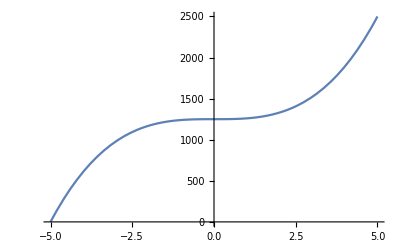

10 (125+x^3)

```mathematica
Plot[
	adjustPotential[x^3, x] /. x -> r,
	{r,  XLEFT, XRIGHT}
]
```

#### potential scaling distribution experiment

```mathematica
MaxValue[{x^2, XLEFT < x < XRIGHT}, {x}]
```

25

```mathematica
MaxValue[{99 UnitStep[x], XLEFT < x < XRIGHT}, {x}]
```

99

## potential forms

### analytic coefficients and translations

### step functions

### sampling and smoothing

## Formatting Solutions

```mathematica
NetModel["Inception V1 Trained on ImageNet Competition Data"]
```

NetChain[]